```mathematica
wcut={0.09817477,0.29452431,0.49087385,0.68722339,0.88357293,1.07992247,1.27627202,1.47262156};
```

```mathematica
Imsigmad244={-0.75695831,-0.8162346,-0.82167243,-0.81380353,-0.80647974,-0.80226536,-0.80196209,-0.80265564};
```

```mathematica
Imsigmad254={-0.79950841,-0.83408479,-0.83104235,-0.82098562,-0.81412963,-0.80763258,-0.80431782,-0.80572404};
```

```mathematica
Imsigmad264={-2.29257715,-1.40008803,-1.16498887,-1.05227171,-0.9909526,-0.95349762,-0.93144621,-0.91909725};
```

```mathematica
Imsigmad274={-2.91454087,-1.62315219,-1.29559014,-1.14618971,-1.06339757,-1.01622667,-0.98609095,-0.96773295};
```

```mathematica
Imsigmad284={-3.11331272,-1.79657692,-1.40901273,-1.23155329,-1.13475042,-1.07577364,-1.03952395,-1.01822722};
```

```mathematica
Imsigmad294={-3.81127608,-1.98994493,-1.52163954,-1.31343478,-1.20321915,-1.13410847,-1.0922615,-1.06483275};
```

```mathematica
Imsigmad244vsw=Table[{wcut[[i]],Imsigmad244[[i]]},{i,1,Length[Imsigmad244]}];
```

```mathematica
Imsigmad254vsw=Table[{wcut[[i]],Imsigmad254[[i]]},{i,1,Length[Imsigmad254]}];
```

```mathematica
Imsigmad264vsw=Table[{wcut[[i]],Imsigmad264[[i]]},{i,1,Length[Imsigmad264]}];
```

```mathematica
Imsigmad274vsw=Table[{wcut[[i]],Imsigmad274[[i]]},{i,1,Length[Imsigmad274]}];
```

```mathematica
Imsigmad284vsw=Table[{wcut[[i]],Imsigmad284[[i]]},{i,1,Length[Imsigmad284]}];
```

```mathematica
Imsigmad294vsw=Table[{wcut[[i]],Imsigmad294[[i]]},{i,1,Length[Imsigmad294]}];
```

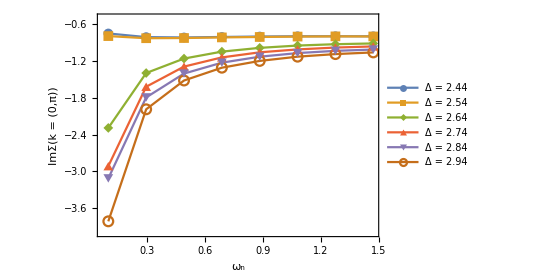

```mathematica
Imsigmavsw=ListPlot[{Imsigmad244vsw,Imsigmad254vsw,Imsigmad264vsw,Imsigmad274vsw,Imsigmad284vsw,Imsigmad294vsw},PlotLegends->Placed[LineLegend[{"Δ = 2.44","Δ = 2.54","Δ = 2.64","Δ = 2.74","Δ = 2.84","Δ = 2.94"},LabelStyle->{13},LegendLayout->{"Row",3}],{0.65,0.25}],PlotMarkers->{Automatic,10},PlotRange->{All,{-3.99,-0.51}},Joined->True,Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->14,FontFamily->"times New Roman"},FrameLabel->{"ω_n","ImΣ(k = (0,π))"}]
```

```mathematica
Export["/Users/cosdis/Desktop/threeband_project/Imsigmavsw.pdf",Imsigmavsw,"PDF"];
```